Last modified on: Monday, July 9, 2018 at 15:03

Author Info

Enrico Castro Grespan

Grankovsky Vladimir

IER-UNAM

Poster Session Content

Rooftop Recognition for Solar Energy Potential

The aim of this project is to detect the rooftop of buildings to determine the available area at different locations and to identify the most suitable ones for solar energy application such as solar PV using Neural Networks and satellite imagery.

Add the most representative image of your project here. (We recommend just 1 image, if you add more, we will make a collage of the images.)

-Graphics--Graphics-

A neural net was trained and tested using a dataset which contained the aerial images of five different cities and their corresponding mask. A mask is a binary image where white pixels tell us where are the building rooftops and a black pixel for the rest of the image. A generator function to load a batch of files into the training was needed to handle the whole dataset. The neural net to trained was chosen from the Semantic Segmentation category at Wolfram Neural Net Repository. “Ademxapp Model A1 Trained on PASCAL VOC2012 and MS-COCO Data” net was modify for the specific needs of the dataset and the classes to return. A good correlation between the test images and their rooftops was obtained.

- Superpose the solar radiation map for solar thermal or PV applications.
- Calculate the ground area of the rooftops.
- Train with high resolution images and masks of other regions of interest.

Note: Everything above this bar is your poster.Make sure it fits on a single page. "Preview Poster"

End of School Presentation Content

In addition to the poster content, include other content to present at the 2 minute presentation for end of school. Use the buttons below to add more sections."Add Header""Add Text""Add Code or Image"

The Dataset

Type text hereAmount: 180 
Size: 5000x5000 
Resolution: 30 cm
Ground truth data for two semantic classes : building and not building

-Graphics-

The net

NetGraph[<>]

Generator

In order to train the net with a big amount of data a generator function was created. The generator function load a single batch of data from an external source to train each time.

partGenerator=Function[Block[{batch,dataSet,batchData},
	If[!ValueQ[partitionedData],partitionedData=Partition[Range[Length[data]],#BatchSize,#BatchSize,1]];
	Print[Association@Thread[Keys[#]→Values[#]]];
	batch=Mod[#AbsoluteBatch,Floor[Length@data/#BatchSize]];
	batchData=data⟦partitionedData[[Echo@(batch+1)]]⟧;
	
	Thread[Keys[batchData]→1+BinaryDeserialize/@Values[batchData]]
]
];

Results

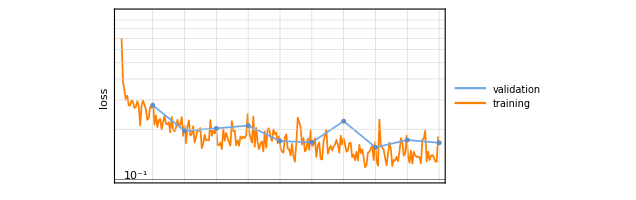
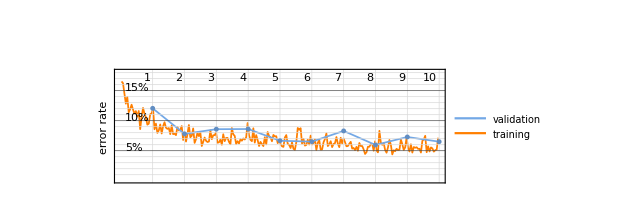

-Graphics-

Note: Everything above this bar is in your 2 minute presentation. Make sure it fits on 2 slides. "Preview Presentation"

Detailed Project Notes

#### Main Results in Detail

The net selected for this project was taken from the Wolfram Neural Net Repository for Semantic Segmentation. Released in 2016 by the University of Adelaide, Ademxapp Model A1 Trained on PASCAL VOC2012 and MS-COCO Data was modify to identify two classes instead of 21.

In order to train the net with a big amount of data a generator function is needed The generator function load a single batch of data from an external source to train each time. NetTrain[net, f, …] calls f at each training batch iteration, thus only keeping a single batch of training data in memory. The function can depend on the batch size, which can be set or set automatic by the computer, the absolute batch that is the number of batches load during the training and the round.

Binary files are a way to reduce of the size while importing the train set. Once the files are binarize the file size reduces and ones read in can be deserialize. At the same time TIF images were converted to JPG to remove unnecessary information while reducing size.

```mathematica
-Graphics--Graphics-
```

#### Code

https://github.com/enricocg/Project

#### Conclusions in Detail

There are two approach to work with neural networks, each approach depends on the two main elements, data and the neural network. It is important to keep in mind both when doing modification and work around this two elements in order to obtain better results.

Create a neural network around your data set

Modify the training data to work on your neural network

Once a neural network created the perfomance of the trained net will depend on the training set.

#### All Visualizations

#### Data Sources Links/References

https://project.inria.fr/aerialimagelabeling/

https://resources.wolframcloud.com/NeuralNetRepository/resources/Ademxapp-Model-A1-Trained-on-PASCAL-VOC2012-and-MS-COCO-Data

#### Future Directions

Superpose the solar radiation map for solar thermal or PV applications.

Calculate the ground area of the rooftops.

Train with high resolution images and masks of other regions of interest.

Improve the functionality for users.

#### Background Info Links/References

http://reference.wolfram.com/language/tutorial/NeuralNetworksLargeDatasets.html

#### Keywords

Provide keywords as items

Neural Networks

Semantic Segmentation

Solar Energy